# Recognizing shapes by training neural networks

#### Part 1

```mathematica
randomRectangle:=Translate[Rectangle[{-.5,-.5},{.5,.5}],RandomReal[{-1,1},2]]
```

```mathematica
randomDisk:=Translate[Disk[{0,0},.5],RandomReal[{-1,1},2]]
```

```mathematica
randomExample[n_]:=Module[{r,p},
Table[
r=RandomInteger[];
p=If[r==0,randomDisk,randomRectangle];
g=Graphics[p,PlotRange->1,Background->Orange];
i=Image[g,ImageSize->{100,100}];
i->If[r==0,"Disk","Rectangle"],
n]
]
```

```mathematica
training=randomExample[2000];
```

```mathematica
net=NetGraph[{
ConvolutionLayer[8,{3,3}],
ElementwiseLayer[Ramp],
PoolingLayer[{3,3},"Stride"->2],
FlattenLayer[],
DotPlusLayer[80],
ElementwiseLayer[Ramp],
DotPlusLayer[2],
SoftmaxLayer[]
},
{1->2->3->4->5->6->7->8},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"Disk","Rectangle"}}]
]
```

NetGraph[]

```mathematica
net=NetInitialize[net];
```

```mathematica
{Last[#],net[First[#]]}&/@randomExample[8]
```

{{Rectangle,Rectangle},{Rectangle,Rectangle},{Disk,Rectangle},{Rectangle,Rectangle},{Rectangle,Rectangle},{Disk,Rectangle},{Disk,Rectangle},{Rectangle,Rectangle}}

```mathematica
result=NetTrain[net,training,TargetDevice->"GPU"]
```

NetGraph[]

```mathematica
result[-Graphics-]
```

Rectangle

```mathematica
validation=randomExample[100];
```

```mathematica
RandomSample[validation,10]
```

{-Graphics-→Disk,-Graphics-→Disk,-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Disk,-Graphics-→Rectangle}

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

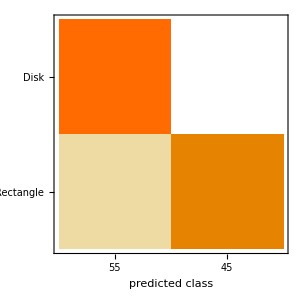

```mathematica
cm["ConfusionMatrixPlot"]
```

#### Part 2

```mathematica
randomRectangle:=Translate[Rectangle[{-.5,-.5},{.5,.5}],RandomReal[{-1,1},2]]
```

```mathematica
randomDisk:=Translate[Disk[{0,0},.5],RandomReal[{-1,1},2]]
```

```mathematica
randomExample[n_]:=Module[{r,p},
Table[
r=RandomInteger[];
p=If[r==0,randomDisk,randomRectangle];
g=Graphics[{RandomColor[],p},PlotRange->1,Background->RandomColor[]];
i=Image[g,ImageSize->{100,100}];
i->If[r==0,"Disk","Rectangle"],
n]
]
```

```mathematica
randomExample[7]
```

{-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Rectangle}

```mathematica
training=randomExample[2000];
```

```mathematica
net=NetGraph[{
ConvolutionLayer[10,{4,4}],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[20,{4,4}],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
FlattenLayer[],
DotPlusLayer[100],
ElementwiseLayer[Ramp],
DotPlusLayer[2],
SoftmaxLayer[]
},
{1->2->3->4->5->6->7->8->9->10->11},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"Disk","Rectangle"}}]
]
```

NetGraph[]

```mathematica
net=NetInitialize[net]
```

NetGraph[]

```mathematica
RandomSample[training,4]
```

{-Graphics-→Disk,-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Rectangle}

```mathematica
result=NetTrain[net,training,TargetDevice->"GPU",MaxTrainingRounds->120]
```

NetGraph[]

```mathematica
result[-Graphics-]
```

Disk

```mathematica
validation=randomExample[100];
```

```mathematica
RandomSample[validation,10]
```

{-Graphics-→Rectangle,-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Rectangle,-Graphics-→Rectangle,-Graphics-→Rectangle,-Graphics-→Rectangle}

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

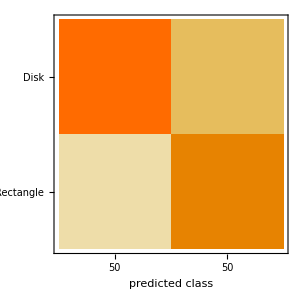

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
validation[[1]]
```

-Graphics-→Rectangle

```mathematica
Dataset[Table[<|"image"->First[v],"actual"->Last[v],"prediction"->result[First[v]],"features"->Map[Image,ng[First[v]]]|>,{v,validation}]]
```

Dataset[<>]

```mathematica
ng=Take[result,{1,1}]
```

NetGraph[]

```mathematica
randomExample[1]
```

{-Graphics-→Rectangle}

```mathematica
Image/@ng[-Graphics-]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}